# Brendan Philbin Several Seeds Analysis

## Import Relevant Files

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
numSweeps=Range[0,100];
colors={Darker[Red],Blue,Darker[Green],Black,Orange};

For[t=1,t≤3,t++,
For[r=0,r≤4,r++,
Evaluate[Symbol["rawTrial" <> ToString[t]<>"r"<>ToString[r]]]=Flatten[Import["several_seeds_output"<>ToString[t]<>"_r"<>ToString[r]<>".csv"]];
Evaluate[Symbol["trial"<>ToString[t]<>"r"<>ToString[r]]]=Transpose[{numSweeps,Evaluate[Symbol["rawTrial"<>ToString[t]<>"r"<>ToString[r]]]}];
Evaluate[Symbol["plot"<>ToString[t]<>"r"<>ToString[r]]]=ListLinePlot[Evaluate[Symbol["trial"<>ToString[t]<>"r"<>ToString[r]]],PlotStyle->colors⟦r⟧];
]
];
```

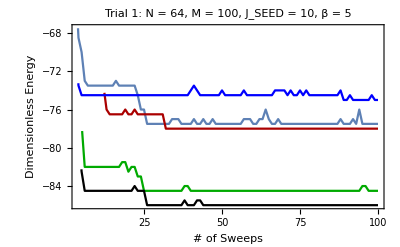

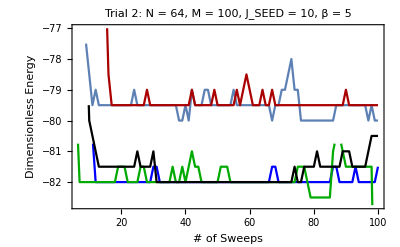

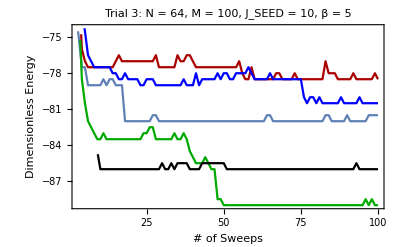

```mathematica
Show[plot1r0,plot1r1,plot1r2,plot1r3,plot1r4,Frame->True,FrameLabel->{"# of Sweeps","Dimensionless Energy"},PlotRange->All,PlotLabel->"Trial 1: N = 64, M = 100, J_SEED = 10, β = 5",LabelStyle->Black]
Show[plot2r0,plot2r1,plot2r2,plot2r3,plot2r4,Frame->True,FrameLabel->{"# of Sweeps","Dimensionless Energy"},PlotRange->All,PlotLabel->"Trial 2: N = 64, M = 100, J_SEED = 10, β = 5",LabelStyle->Black]
Show[plot3r0,plot3r1,plot3r2,plot3r3,plot3r4,Frame->True,FrameLabel->{"# of Sweeps","Dimensionless Energy"},PlotRange->All,PlotLabel->"Trial 3: N = 64, M = 100, J_SEED = 10, β = 5",LabelStyle->Black]
```